Requires the routine in visualize_results2d.nb to be run

## Routines for lists of solution

### Error Computation

```mathematica
(*data is a list of moment theories for which the error has to be computed and ref is the data for the reference moment theory with respect to which the error has to be computed.*)

ComputeRelativeErrorL2[data_,ref_,domain_]:=Module[{result},
result = Sqrt[NIntegrate[(data-ref)^2,domain]];

result
]
```

### Import Solution

```mathematica
(*Given a list of  degrees of freedom we read a list of data from it*)
ImportList[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result},

If[Length[dof]≠ Length[outputdir],Print[Style["Incorrect Input Data",FontColor->Red]]];

result = Table[importdata[dof⟦ii⟧,p,refinetype,flag,outputdir⟦ii⟧],{ii,1,Length[dof]}];

result
]
```

### Convert To Prim

```mathematica
ConvToPrimList[sol_]:=Module[{result},
result = Table[ConvToPrim[ii],{ii,sol}];
result
]
```

### Interpolate List

```mathematica
InterpolateSolutionList[solution_]:=Module[{result},
result =Table[ InterpolateSolution[ii],{ii,solution}];
result
]
```

### Compute Difference

```mathematica
(*Given a list, the following routine returns a list containing the difference between the difference elements and scales the value with the maximum value in the list*)
DifferenceList[data_]:=Module[{result},
result = Table[Abs[data⟦ii-1⟧-data⟦ii⟧],{ii,2,Length[data]}]/Max[data];

result
]
```

## Heated Cavity (M Adaptive)

### Pre Processing

```mathematica
ndof={1300,5200,20800};
foldername = "Tests/build/output_N6_heated_cavity_2D_Kn0p1";
numsol20=ImportList[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrimList[numsol20];
solution20 = InterpolateSolutionList[numsol20];

ndof={2200,8800,35200};
foldername = "Tests/build/output_N9_heated_cavity_2D_Kn0p1";
numsol35=ImportList[ndof,1,"_global_",0,foldername];
numsol35 = ConvToPrimList[numsol35];
solution35 = InterpolateSolutionList[numsol35];

ndof={2800,11200,44800};
foldername = "Tests/build/output_N11_heated_cavity_2D_Kn0p1";
numsol45=ImportList[ndof,1,"_global_",0,foldername];
numsol45 = ConvToPrimList[numsol45];
solution45 = InterpolateSolutionList[numsol45];


ndof={3400,13600,54400};
foldername = "Tests/build/output_N12_heated_cavity_2D_Kn0p1";
numsol56=ImportList[ndof,1,"_global_",0,foldername];
numsol56 = ConvToPrimList[numsol56];
solution56 = InterpolateSolutionList[numsol56];


(*
ndof=13600;
foldername = "Tests/build/output_N12_heated_cavity_2D_Kn0p1";
numsol56=importdata[ndof,1,"_global_",0,foldername];
numsol56 = ConvToPrim[numsol56];
solution56 = InterpolateSolution[numsol56];

ndof=17200;
foldername = "Tests/build/output_N15_heated_cavity_2D_Kn0p1";
numsol71=importdata[ndof,1,"_global_",0,foldername];
numsol71 = ConvToPrim[numsol71];
solution71 = InterpolateSolution[numsol71];

ndof=20000;
foldername = "Tests/build/output_N16_heated_cavity_2D_Kn0p1";
numsol84=importdata[ndof,1,"_global_",0,foldername];
numsol84 = ConvToPrim[numsol84];
solution84 = InterpolateSolution[numsol84];*)
```

### Error Computation

```mathematica
L2Error={ComputeRelativeErrorL2[solution20⟦All,1⟧,solution56⟦-1,1⟧],ComputeRelativeErrorL2[solution35⟦All,1⟧,solution56⟦-1,1⟧],ComputeRelativeErrorL2[solution45⟦All,1⟧,solution56⟦-1,1⟧]};
```

```mathematica
L2ErrorDifference = Flatten[ConstantArray[0,{3}]];
Do[L2ErrorDifference⟦ii⟧=DifferenceList[L2Error⟦ii⟧];,{ii,1,Length[L2Error]}];
```

```mathematica
L2ErrorDifference
```

{{0.0203665,0.00557753},{0.0207427,0.0251857},{0.461298,0.170682}}

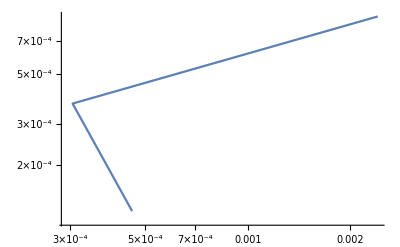

```mathematica
ListLogLogPlot[L2ErrorDifference,Joined->True]
```

```mathematica
L2Error
```

{{0.0219713,0.0224281,0.022303},{0.0147114,0.0144062,0.0140357},{0.00523211,0.00281855,0.00192552}}

### Results

#### Uniform Refinement

```mathematica
ndof={5200};
foldername = "Tests/build/output_N6_heated_cavity_2D_Kn0p1";
numsol20=ImportList[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrimList[numsol20];
solution20 = InterpolateSolutionList[numsol20];

ndof={220000};
foldername = "Tests/build/output_N9_heated_cavity_2D_Kn0p1";
numsol35=ImportList[ndof,1,"_global_",0,foldername];
numsol35 = ConvToPrimList[numsol35];
solution35 = InterpolateSolutionList[numsol35];

ndof={280000};
foldername = "Tests/build/output_N11_heated_cavity_2D_Kn0p1";
numsol45=ImportList[ndof,1,"_global_",0,foldername];
numsol45 = ConvToPrimList[numsol45];
solution45 = InterpolateSolutionList[numsol45];


ndof={13600};
foldername = "Tests/build/output_N12_heated_cavity_2D_Kn0p1";
numsol56=ImportList[ndof,1,"_global_",0,foldername];
numsol56 = ConvToPrimList[numsol56];
solution56 = InterpolateSolutionList[numsol56];
```

Reading Data from...

../Tests/build/output_N6_heated_cavity_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_5200

Reading Data from...

../Tests/build/output_N9_heated_cavity_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_220000

Reading Data from...

../Tests/build/output_N11_heated_cavity_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_280000

Reading Data from...

../Tests/build/output_N12_heated_cavity_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_13600

#### Adaptive

```mathematica
(*different degrees of freedom*)
ndof = {141736,170368,191560,202816,222904,234400};
filename={"Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p2","Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p1",
"Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p08",
"Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p07",
"Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p05",
"Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p04"};

Quiet[solutionAdaptive = Table[importdata[ndof⟦ii⟧,1,"_global_",0,filename⟦ii⟧],{ii,1,Length[filename]}]];

Quiet[FeIndexAdaptive = Table[importdata[ndof⟦ii⟧,1,"_global_",4,filename⟦ii⟧],{ii,1,Length[filename]}]];
```

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p2/solution/numerical_solution_global_degree_1_DOF_141736

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p1/solution/numerical_solution_global_degree_1_DOF_170368

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p08/solution/numerical_solution_global_degree_1_DOF_191560

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p07/solution/numerical_solution_global_degree_1_DOF_202816

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p05/solution/numerical_solution_global_degree_1_DOF_222904

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p04/solution/numerical_solution_global_degree_1_DOF_234400

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p2/solution/fe_index_global_degree_1_DOF_141736

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p1/solution/fe_index_global_degree_1_DOF_170368

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p08/solution/fe_index_global_degree_1_DOF_191560

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p07/solution/fe_index_global_degree_1_DOF_202816

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p05/solution/fe_index_global_degree_1_DOF_222904

Reading Data from...

../Tests/build/output_N6_N9_N11_N12_heated_cavity_adaptive_2D_Kn0p1_frac0p04/solution/fe_index_global_degree_1_DOF_234400

```mathematica
solutionAdaptive = ConvToPrimList[solutionAdaptive];
numsolAdaptive = InterpolateSolutionList[solutionAdaptive];
```

```mathematica
Quiet[L2ErrorAdaptive = ComputeRelativeErrorL2[numsolAdaptive⟦All,IDtheta-2⟧,solution56⟦1,IDtheta-2⟧]];
```

```mathematica
L2ErrorAdaptive
```

{0.0125893,0.0108679,0.0106195,0.0102901,0.00934049,0.00867615}

### Plots

```mathematica
ListPlot3D[numsol45⟦1⟧⟦All,{1,2,IDqy+20}⟧,PlotRange->Full]
```

Part::partw: Part {1,2,31} of {-0.5,-0.5,-1.03901,-0.000133,-0.000133,1.04115,0.00209869,0.0140516,0.00209869,-0.0761935,-0.0761935,0.004524,«6»,-0.002526,0.000607,-0.000578,-0.000129,-0.000578,0.000607,0.004978,0.004978,-0.004181,0.003128,0.003128,-0.004181} does not exist.

ListPlot3D::arrayerr: {«1»}⟦All,{1,2,31}⟧ must be a valid array or a list of valid arrays.

ListPlot3D[{1}⟦All,{1,2,31}⟧,PlotRange→Full]
 |  |  |  |

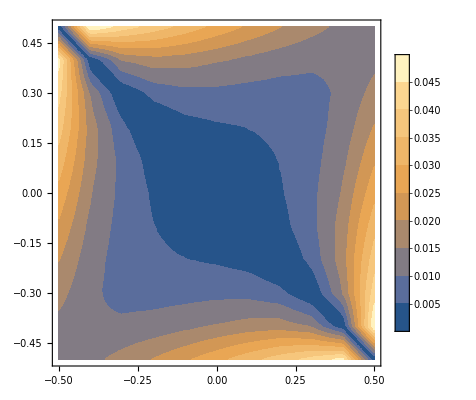

```mathematica
ContourPlot[Abs[solution20⟦1,IDtheta-2⟧[x,y]-solution56⟦1,IDtheta-2⟧[x,y]],{x,-0.5,0.5},{y,-0.5,0.5},PlotLegends->Automatic,PlotRange->Full,ContourLines->False]
```

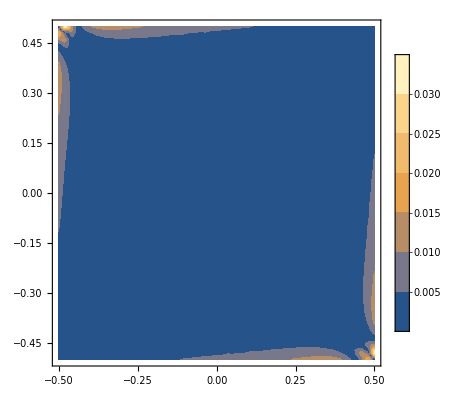

```mathematica
ContourPlot[Abs[solution45⟦1,IDtheta-2⟧[x,y]-solution56⟦1,IDtheta-2⟧[x,y]],{x,-0.5,0.5},{y,-0.5,0.5},PlotLegends->Automatic,PlotRange->Full,ContourLines->False]
```

## Poisson Heat Conduction

### Results

#### Uniform Refinement

```mathematica
ndof={10400};
foldername = {"Tests/build/output_N6_poisson_heat_conduction_adaptive_2D_Kn0p1"};
numsol20=ImportList[ndof,1,"_global_",0,foldername];

(*Convert the data to primitive solutions*)
numsol20 = ConvToPrimList[numsol20];

(*Interpolate solution for plotting*)
solution20 = InterpolateSolutionList[numsol20];

ndof={27200};
foldername = {"Tests/build/output_N12_poisson_heat_conduction_adaptive_2D_Kn0p1"};
numsol56=ImportList[ndof,1,"_global_",0,foldername];
numsol56 = ConvToPrimList[numsol56];
solution56 = InterpolateSolutionList[numsol56];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_adaptive_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_10400

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_adaptive_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_27200

InterpolatingFunction::dmval: Input value {0,-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

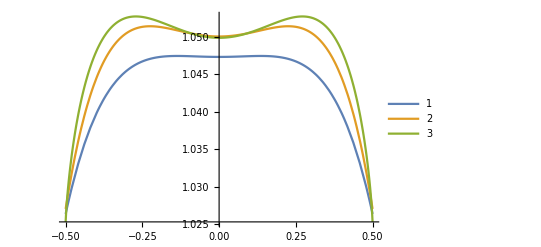

```mathematica
Plot[{solution20⟦1,IDtheta-2⟧[0,y],solution56⟦1,IDtheta-2⟧[0,y],θExactKn0p1[y]},{y,-0.5,0.5},PlotLegends->Automatic]
```

```mathematica
errorUniformRefine ={ {10400,ComputeRelativeErrorL2[solution20⟦1,IDtheta-2⟧[0,y],θExactKn0p1[y],{y,-0.5,0.5}]},{22400,ComputeRelativeErrorL2[solution45⟦1,IDtheta-2⟧[0,y],θExactKn0p1[y],{y,-0.5,0.5}]}};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.419906}. NIntegrate obtained 0.0000329169 and 6.01855×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.417984}. NIntegrate obtained 2.0467×10^-6 and 2.13602×10^-11 for the integral and error estimates.

#### Adaptive

```mathematica
(*different degrees of freedom*)
ndof = {31560};
filename={"/Tests/build/output_N6_N12_poisson_heat_conduction_adaptive_2D_Kn0p1"};

solutionAdaptive = ImportList[ndof,1,"_global_",0,filename];
FEAdaptive = importdata[ndof⟦1⟧,1,"_global_",4,filename⟦1⟧];
```

Reading Data from...

..//Tests/build/output_N6_N12_poisson_heat_conduction_adaptive_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_31560

Reading Data from...

..//Tests/build/output_N6_N12_poisson_heat_conduction_adaptive_2D_Kn0p1/solution/fe_index_global_degree_1_DOF_31560

```mathematica
solutionAdaptive = ConvToPrimList[solutionAdaptive];
numsolAdaptive = InterpolateSolutionList[solutionAdaptive];
```

InterpolatingFunction::dmval: Input value {0,-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

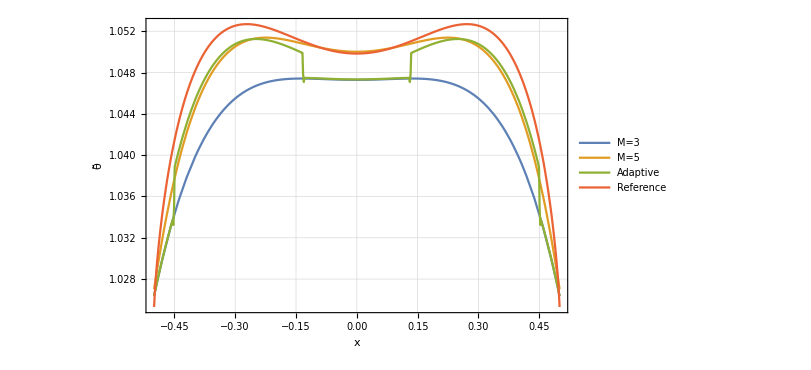

```mathematica
Plot[{solution20⟦1,IDtheta-2⟧[0,x],temperatureFullKn0p1[12][x],numsolAdaptive⟦1,IDtheta-2⟧[0,x],θExactKn0p1[x]},{x,-0.5,0.5},ImageSize->600,GridLines->Automatic,Frame->True,FrameTicksStyle->18,PlotLegends->{"M=3","M=5","Adaptive","Reference"},FrameLabel->{{Style["θ̃",18],None},{Style["x",18],None}},RotateLabel->False]
```

InterpolatingFunction::dmval: Input value {0,-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

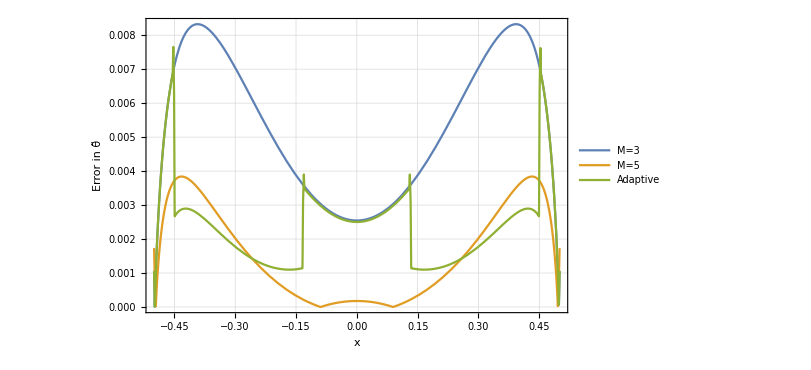

```mathematica
Plot[{Abs[solution20⟦1,IDtheta-2⟧[0,x]-θExactKn0p1[x]],
Abs[temperatureFullKn0p1[12][x]-θExactKn0p1[x]],Abs[numsolAdaptive⟦1,IDtheta-2⟧[0,x]-θExactKn0p1[x]]},{x,-0.5,0.5},ImageSize->600,GridLines->Automatic,Frame->True,FrameTicksStyle->18,PlotLegends->{"M=3","M=5","Adaptive","Reference"},FrameLabel->{{Style["Error in θ̃",18],None},{Style["x",18],None}},RotateLabel->True]
```